## Setup

### Directory setup

```mathematica
(* Silence warning for NaN values *)
(*SetSystemOptions["LibraryLinkOptions"->"TestFloatingPointExceptions"->False];*)
```

```mathematica
SetDirectory["C:/Users/user/Desktop/Coding/ant/data/sleap"]
```

C:\Users\user\Desktop\Coding\ant\data\sleap

```mathematica
file=Import["testset.hdf5","Data"];
```

```mathematica
src=file⟦"/trajectory_0"⟧;
```

```mathematica
imgsize=Max[{xmax,ymax}];
scalefactor=imgsize/17.5(*pixels per cm*)
```

0.0571429 Max[xmax,ymax]

### Probability Distribution Functions

```mathematica
(* Necessary for computing probability assigned with step coordinate pairs. Functions were generated from unconditioned single ant data. With more data this should be elaborated to conditional probability to provide better prediction. *)
```

```mathematica
avdist=DataDistribution[…];
```

```mathematica
speeddist=DataDistribution[…];
```

### Initialize

```mathematica
list={};
Do[
src=file⟦n+Length[file]/2⟧;
frames=file⟦n⟧;
head=src⟦;;,1⟧;
thorax=src⟦;;,2⟧;
abdomen=src⟦;;,3⟧;
Do[
If[head⟦1,m⟧>1,
(*skip*),
head⟦1,m⟧=head⟦1,m-1⟧;
];
If[head⟦2,m⟧>1,
(*skip*),
head⟦2,m⟧=head⟦2,m-1⟧
]
,{m,1,Length[head⟦1⟧]}];
Do[
If[thorax⟦1,m⟧>1,
(*skip*),
thorax⟦1,m⟧=thorax⟦1,m-1⟧;
];
If[thorax⟦2,m⟧>1,
(*skip*),
thorax⟦2,m⟧=thorax⟦2,m-1⟧
]
,{m,1,Length[thorax⟦1⟧]}];
Do[
If[abdomen⟦1,m⟧>1,
(*skip*),
abdomen⟦1,m⟧=abdomen⟦1,m-1⟧;
];
If[abdomen⟦2,n⟧>1,
(*skip*),
abdomen⟦2,m⟧=abdomen⟦2,m-1⟧
]
,{m,1,Length[abdomen⟦1⟧]}];
avg=(head+thorax+abdomen)/3.;
avg=PrependTo[avg,frames];
AppendTo[list,avgᵀ];

(*Length[file] is always an even number, because the converter creates one table for trajectory and one table for frame numbers for every SLEAP trajectory in the input file.*)
,{n,1,Length[file]/2}]
```

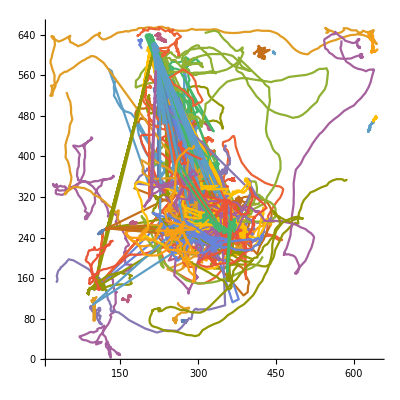

```mathematica
ListPlot[list⟦;;,;;,2;;3⟧,PlotRange->All,Joined->True,ImageSize->Full,AspectRatio->1]
```

## Jump counts/disconnect trajectories

```mathematica
Module[{jump,θ=15.1},
ct=0;
pruned={};
Do[
jump=1;
sc=0;
Do[
If[
Norm[list⟦i,j,2;;3⟧-list⟦i,j-1,2;;3⟧]>θ,
AppendTo[pruned,list⟦i,jump;;j-1⟧];
jump=j;
sc+=1;
ct+=1];
,{j,2,Length[list⟦i⟧]}];
If[sc==0,
AppendTo[pruned,list⟦i⟧];
ct+=1],
{i,1,Length[list]}]
];
```

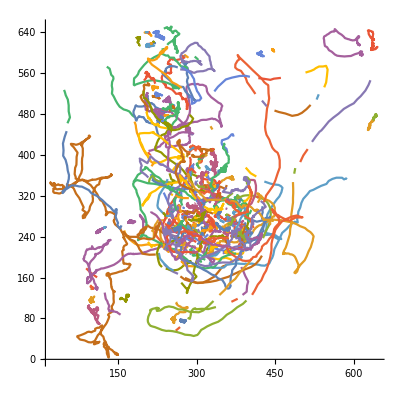

```mathematica
tr=ListPlot[pruned⟦;;,;;,2;;3⟧,PlotRange->All,Joined->True,ImageSize->Full,AspectRatio->1]
```

## Probability-based prediction visualized

```mathematica
position=pruned⟦37,-1,2;;3⟧;
pposition=pruned⟦37,-2,2;;3⟧;
xval=position⟦1⟧;yval=position⟦2⟧;
x1val=pposition[[1]];y1val=pposition[[2]];
initangle=OriAnt[position,pposition];
```

```mathematica
ArcCos2[300-xval,300-yval]
```

### Single step

#### Angle-only probability view

```mathematica
DensityPlot[PDF[avdist,Mod[ArcCos2[x-xval,y-yval]-initangle+π,2π]-π],{x,0,700},{y,0,700},PlotLegends->Automatic,PlotRange->Full,PlotPoints->200,MaxRecursion->5,PlotLabel->"Probability of next step angle for sample position"]
```

```mathematica
Plot[PDF[avdist,θ],{θ,-π,π},PlotRange->All]
```

#### Stepsize-only probability view

```mathematica
DensityPlot[PDF[speeddist,Sqrt[(x-xval)^2+(y-yval)^2]/scalefactor],{x,0,700},{y,0,700},PlotRange->All,PlotPoints->100,PlotLabel->"Probability of distance to next step for sample position"]
```

#### Combined probability view

```mathematica
DensityPlot[PDF[speeddist,Sqrt[(x-xval)^2+(y-yval)^2]/scalefactor]PDF[avdist,Mod[ArcCos2[x-xval,y-yval]-initangle+π,2π]-π],{x,0,700},{y,0,700},PlotRange->All,PlotPoints->100,PlotLabel->"Probability of distance to next step for sample position"]
```

```mathematica
DensityPlot[PDF[speeddist,Sqrt[(x-xval)^2+(y-yval)^2]/scalefactor]PDF[avdist,Mod[ArcCos2[x-xval,y-yval]-initangle+π,2π]-π],{x,xval-100,xval+100},{y,yval-100,yval+100},PlotRange->All,PlotPoints->50,MaxRecursion->15,PlotLabel->"Probability of distance to next step for sample position"]
```

### Two-steps

```mathematica
probrepeat=1;
dp=DensityPlot[PDF[speeddist,Sqrt[(x-xval)^2+(y-yval)^2]/(10probrepeat)]^probrepeat PDF[avdist,(Mod[ArcCos2[x-xval,y-yval]-initangle+π,2π]-π)/probrepeat]^probrepeat,{x,0,700},{y,0,700},PlotRange->All,PlotPoints->300,MaxRecursion->15,PlotLegends->Automatic,PlotLabel->"Probability of distance to next step for sample position",ImageSize->Full]
```

#### Overlay

```mathematica
Show[dp,part1,part2]
```

## Probability-based prediction compute

### Helper function

```mathematica
ArcCos2[x_,y_]:=Module[
{ans,temp,norm},
norm=Sqrt[x^2+y^2];
If[y<0,
ans=ArcCos[x/norm],
ans=-ArcCos[x/norm];
];
Return[ans]
]
```

```mathematica
OriAnt[ultim_,penultim_]:=Module[{x1,y1,x2,y2,dx,dy,norm,angle},
x1=penultim⟦1⟧;
x2=ultim⟦1⟧;
y1=penultim⟦2⟧;
y2=ultim⟦2⟧;
dx=x2-x1;
dy=y2-y1;
norm=Sqrt[dx^2+dy^2]+0.0001;
angle=ArcCos2[dx/norm,dy/norm];
Return[angle];
]
```

```mathematica
Hungarian[sources_,targets_]:=Module[{src,tgt,presrc,prob,size,costmatrix,invprob,boolmat,zerocount,zero,minrow,markedzeros,markedrows,markedcolumns,unmarkedrows,unmarkedzeros,markedtotal,
solved=False, (*Iteration criterion*)
searchrange=5 (* How far into future should the trajectory linker look to for search? *)
},

(*
Initialization.
1. Define the size as the longer of the two dimensions between sources and targets.
2. Create a square matrix with the size as chosen above.
3. Subtract match probability from this square matrix.
4. The 'padding' elements can be left at initial value.
This part corresponds to lines 1-8 in the line-by-line pseudocode in notes.
*)

size=Max[{Length[sources],Length[targets]}];
(*It is necessary to define costmatrix as square matrix first because we need a bijective mapping for linear sum assignment algorithms to work *)
costmatrix=ConstantArray[1,{size,size}];
Do[
(*Get source, pre-source and target coordinates*)
src=pruned⟦sources⟦i⟧,-1⟧;
presrc=pruned⟦sources⟦i⟧,-2⟧;
tgt=pruned⟦targets⟦j⟧,1⟧;
(* If target is outside search range or if target has timestamp earlier than source, then assign 0 for probability. *)
prob=0;
If[tgt⟦1⟧<src⟦1⟧+searchrange,
If[tgt⟦1⟧-src⟦1⟧>0,
prob=GetProb[presrc,src,tgt]]];
costmatrix⟦i,j⟧=1-prob;
,{i,1,Length[sources]},{j,1,Length[targets]}];

Print["Costmatrix"];
Print[costmatrix//MatrixForm];

(*Subtract minima from each row*)
Do[costmatrix⟦i⟧=costmatrix⟦i⟧-Min[costmatrix⟦i⟧],{i,1,size}];
(*Subtract minima from each column*)
Do[costmatrix⟦;;,j⟧=costmatrix⟦;;,j⟧-Min[costmatrix⟦;;,j⟧],{j,1,size}];
(*
Initiate loop for linear assignment.
1. Select particular zero elements and save them as marked zeros.
2. Check whether the marked zeros complete the assignment problem.
3. If it works, then return the marked zeros and terminate.
4. If not, modify the cost matrix and try again.
The entire loop corresponds to the repeating lines 9 through to 56 in the notes.
*)

(* This loop count is included to prevent infinite loops during debugging *)
loop=0;
While[(!solved)∧(loop<(20size)),
loop+=1;

(* Make an N by N boolean matrix where the zeros are marked with True and others by False *)
boolmat=ConstantArray[False,{size,size}];
Do[If[costmatrix⟦i,j⟧==0,boolmat⟦i,j⟧=True],{i,1,size},{j,1,size}];

(* Create a store for marked zeros. *)
markedzeros={};

(*
Initiate loop to mark zeros.
1. Select row with fewest zeros.
2. Pick the first zero in such row and save its row, column number. Include this zero in marked_zeros.
3. Repeat until boolean matrix has no True elements.
This loop corresponds to repeating lines 10 through to 18 in the notes.
*)

(* Check whether boolmat contains any True valued elements. *)
While[MemberQ[Flatten@boolmat,True],
(* Count the number of True in boolmat (equal to number of zeros in the cost matrix) *)
zerocount=Table[Count[boolmat⟦i⟧,True],{i,1,size}];
(* Select the row with fewest nonzero number of True's *)
minrow=Select[Range[size],zerocount⟦#⟧≠0&]⟦1⟧;
(* Select the first zero element on the chosen row. The 'zero' variable is its column index. *)
zero=Select[Range[size],boolmat⟦minrow,#⟧==True&,1]⟦1⟧;
(* I want to eat chicken. *)
iwanttoeatchicken=True;
(* Save the row and column index of the zero to markedzero list. *)
markedzeros=AppendTo[markedzeros,{minrow,zero}];
(* On the boolean matrix, set all elements on the selected row and column as False. *)
boolmat⟦minrow,;;⟧=ConstantArray[False,{size}];
boolmat⟦;;,zero⟧=ConstantArray[False,{size}];
];

(* Reset the boolmat since we turned all of its entries to False in the above loop. *)
boolmat=ConstantArray[False,{size,size}];
Do[If[costmatrix⟦i,j⟧==0,boolmat⟦i,j⟧=True],{i,1,size},{j,1,size}];

(* Mark rows and columns to attempt to complete the assignment.
1. Save rows/columns of the marked zeros on respective lists.
2. Save any rows not included in such list onto a different list for unmarkedrows.
3. Zero elements on unmarked rows are identified and their column values are marked.
4. If the row and column are both marked for some element, label the row as unmarked.
5. Iterate 2~4 until all rows and columns are populated into appropriate list.
6. Any row that isn't in unmarked rows are added to marked rows.
This module corresponds to steps 19 through to 41 on the notes.
*)
Module[{zerorows,zerocols,switch,selectedrow,row,col},

(*Reset the markedcolumns and markedrow list everytime matrix is adjusted*)
markedrows={};

(* Identify row numbers of marked zeros *)
zerorows=markedzeros⟦;;,1⟧;
(* Identify column numbers of marked zeros *)
zerocols=markedzeros⟦;;,2⟧;
(* Select all rows that are not in zerorows. *)
unmarkedrows=Select[Range[size],!MemberQ[zerorows,#]&];

(* Create a new list to store marked columns. *)
markedcolumns={};


switch=True;
(* Main loop for marking rows/columns. *)
While[switch,
(* Disable the repeat switch immediately so that loop doesn't continue unless new assignment is possible. *)
switch=False;

(* First nested stack *)
Do[
(* Iterate through unmarked rows *)
row=unmarkedrows⟦i⟧;
selectedrow=boolmat⟦row⟧;
Do[
(* Iterate through each columns *)
If[
(* Check whether the jth element is True and j is not already in markedcolumns *)
selectedrow⟦j⟧==True∧!MemberQ[markedcolumns,j],
(* Add j to markedcolumns and enable switch to check for other possible assignment. *)
markedcolumns=AppendTo[markedcolumns,j];
switch=True;
]
,{j,1,size}]
,{i,1,Length[unmarkedrows]}];

(* Second nested stack *)
Do[
(* Iterate through each marked zeros *)
row=markedzeros⟦n,1⟧;
col=markedzeros⟦n,2⟧;
If[
(* Check if the marked zero element's row and column are both marked. *)
!MemberQ[unmarkedrows,row]∧MemberQ[markedcolumns,col],
(* If so then place the corresponding row into the list of unmarked rows. *)
unmarkedrows=AppendTo[unmarkedrows,row];
switch=True;
]
,{n,1,Length@markedzeros}]
];
(* Once the loop is done, unmarkedrows and markedcolumns are fully populated. Lastly, populate markedrows by selecting the complement set of unmarkedrows. *)
markedrows=Select[Range[size],!MemberQ[unmarkedrows,#]&];

(*Check the total number of marked rows and columns*)
markedtotal=Length[markedrows]+Length[markedcolumns];
];

If[markedtotal==size,
(* If it matches the size of the matrix, disable while loop and return the result. *)
solved=True;
Return[markedzeros],
(* If it does not match the size of matrix, modify the matrix and try again. *)
costmatrix=AdjustMatrix[costmatrix,markedrows,markedcolumns,size];
]];
]
```

### Matrix Adjuster

```mathematica
AdjustMatrix[matrix_,markedrows_,markedcolumns_,size_]:=Module[{nonmarked,values,minval,modmatrix},
(* Create storage for all elements not in either marked rows or marked columns. *)
nonmarked={};

(* Iterate through each row and column. If row and column are not found in markedrow/markedcolumn lists, then add the row/column pair to list of unmarked values. *)
Do[
If[!MemberQ[markedrows,i]∧!MemberQ[markedcolumns,j],
nonmarked=AppendTo[nonmarked,{i,j}];
],{i,1,size},{j,1,size}];

(* Convert the coordinate of unmarked values to unmarked values themselves. *)
values=Table[matrix⟦nonmarked⟦i,1⟧,nonmarked⟦i,2⟧⟧,{i,1,Length@nonmarked}];

(* Find the minimum among unmarked values. *)
minval=Min[values];

(* Create a new copy of cost matrix for modification. *)
modmatrix=matrix;

(*Check each matrix position; if position is not a marked position, subtract minimum non-marked value. If position falls in both a marked row and a marked column, add minimumn non-marked value.*)
Do[
If[MemberQ[nonmarked⟦;;,1⟧,i]∧MemberQ[nonmarked⟦;;,2⟧,j],
modmatrix⟦i,j⟧-=minval,
If[MemberQ[markedrows,i]∧MemberQ[markedcolumns,j],
 modmatrix⟦i,j⟧+=minval]];
,{i,1,size},{j,1,size}];

(* Return the modified matrix for next iteration of main loop. *)
Return[modmatrix]];
```

### Obtain probabilities

#### Save probability as array

```mathematica
(* The output structure is unnecessarily complicated and was cause of an error in the main compute loop, so this module was deprecated in favor of the Function version of the same code written immediately below. *)
```

```mathematica
Module[{selected,selecteds,ultim,penultim,orientation,prob,probs,nsteps},
probs={};
selecteds={};
ct=0;
Do[
probs=AppendTo[probs,{}];
selecteds=AppendTo[selecteds,{}];
If[Length[pruned⟦n⟧]>1,
penultim=pruned⟦n,-2⟧;
ultim=pruned⟦n,-1⟧;
orientation=OriAnt[ultim,penultim];
Do[
prob={};
selected=Select[pruned,#⟦1,1⟧==t&];
Do[nsteps=t-Max[pruned⟦n,-1,1⟧];
prob=AppendTo[prob,PDF[speeddist,1/(10nsteps)Sqrt[(selected⟦m,1,2⟧-ultim⟦2⟧)^2+(selected⟦m,1,3⟧-ultim⟦3⟧)^2]]^nsteps
PDF[avdist,1/nsteps(Mod[ArcCos2[(selected⟦2⟧-ultim⟦2⟧)/100,(selected⟦3⟧-ultim⟦3⟧)/100]-orientation+π,2π]-π)]^nsteps ];
,{m,1,Length[selected]}];
probs⟦-1⟧=AppendTo[probs⟦-1⟧,prob];
selecteds⟦-1⟧=AppendTo[selecteds⟦-1⟧,selected];
,{t,Max[pruned⟦n,-1,1⟧]+1,Max[pruned⟦n,-1,1⟧]+11}]]
,{n,1,Length[pruned]}];
probsout=probs;
selectedout=selecteds;
]
```

#### GetProb function

```mathematica
(*
Uses penultimate and ultimate positions of source trajectory and the initial position of target trajectory to compute the probability that the two trajectories are contiguous together.
As of now, the function requires that the source trajectory is at least two subsequent steps long because the reliability of orientation obtained from body segment position is not verified. Eventually orientation should be computed by finding direction vector between body segments, so that a singleton trajectory can be integrated properly as well.
*)
```

```mathematica
GetProb[source1_,source_,target_]:=Module[
{probability,tdiff,speed,angular},
tdiff=target⟦1⟧-source⟦1⟧;
(* Finds probability for given displacement over tdiff frames *)
speed=PDF[speeddist,1/(10tdiff)Sqrt[(target⟦2⟧-source⟦2⟧)^2+(target⟦3⟧-source⟦3⟧)^2]]^tdiff;
(* Finds probability for given angular deviation over tdiff frames *)
angular=PDF[avdist,1/tdiff(Mod[ArcCos2[(target⟦2⟧-source⟦2⟧)/100,(target⟦3⟧-source⟦3⟧)/100]-OriAnt[source⟦2;;3⟧,source1⟦2;;3⟧]+π,2π]-π)]^tdiff;
(* Multiply the two *)
probability= speed angular;
Return[probability]
]
```

### Join trajectories

#### Pick maximum

```mathematica
Module[{sources,targets,linklabel,linked},
(*
algorithm:
 1. Iterate through each frame
2. At the given frame, look for all trajectories that end at that time.
3. At the subsequent frame, look for all trajectories that begin at that time.
4. For each target, find the source that has best likelihood for the target.
5. Repeat until all targets are assigned.
6. Proceed to the next frame, carrying over any unmatched trajectory from previous frame.
7. If a trajectory termination point goes unmatched for longer than 5 frames, remove it from the trajectories.
*)
sources={};
targets={};
Do[
(*Comment out the following two lines to make the source/target lists cumulative*)
sources={};
targets={};
Do[
If[pruned⟦n,-1,1⟧==t,
If[Length[pruned⟦n⟧]>1,
AppendTo[sources,n]]
];
If[pruned⟦n,1,1⟧==t+1,
AppendTo[targets,n]
],{n,1,Length[pruned]}];
If[Min[Length[sources],Length[targets]]>0,
assign=Hungarian[sources,targets]];
,{t,66,66}];
]
```

Costmatrix

(0.999969 | 1. | 0.882121 | 0.994885 | 1.
1. | 1. | 1. | 1. | 1.
0.999796 | 0.996258 | 0.999944 | 0.999778 | 0.994447
0.963325 | 0.992622 | 0.999739 | 0.871705 | 0.999546
0.743881 | 0.987901 | 1. | 0.998478 | 0.993385)

```mathematica
Length[assign]
```

4

### Notes for debugging

```mathematica
(*
For {t,66,66}, the cost matrix is a 5x5 array, and the output (named assign) should be five x-y pairs. With the current bug, one coordinate pair (5,2) is omitted.

The issue seems to occur more frequently with the presence of rows or columns with a lot of zeros (for example, row 2 in the case of t=66).

The bug can result in omission of more than one coordinate pairs in the case of larger arrays. For example, when the source/target resets are commented out in the nested loop and the code is run from {t,1,67}, the costmatrix becomes a 102x102 array, while the output is only 97 coordinate pairs. In this case, we can't just guess what the missing coordinate pairs are and so this is problematic.

NOTE: When running the code cumulatively (i.e. without resetting sources/targets lists for every t), it's recommended to comment out the Print statements under the first codeblock inside Hungarian[] function, to prevent mathematica getting stuck trying to write a lot of very long output.
*)
```